```mathematica
d = Transpose[Import["~/zeca-results-all-cell/zeca-results-all-cell/Top8000-best_hom50_pdb_chain/rose_special_charged/run_10000/tmp"]];
```

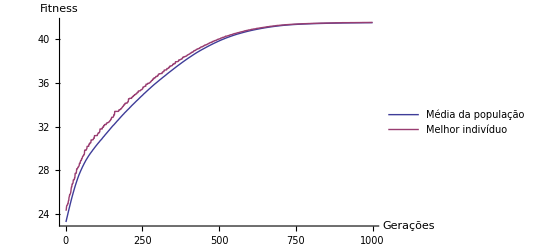

```mathematica
p =ListLinePlot[d, PlotTheme->"Classic", AxesLabel->{"Gerações", "Fitness"}, PlotLegends->{"Média da população", "Melhor indivíduo"}]
```

```mathematica
Export["~/Documentos/PhD-Quali/latex/quali/figures/evo_Eda.pdf", p]
```

~/Documentos/PhD-Quali/latex/quali/figures/evo_Eda.pdf